```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.

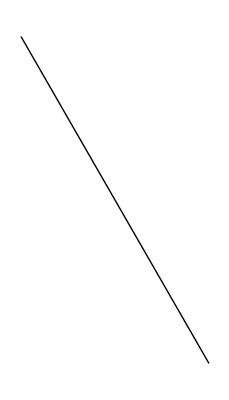

```mathematica
Graphics[Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}], ImageSize->Tiny]
```

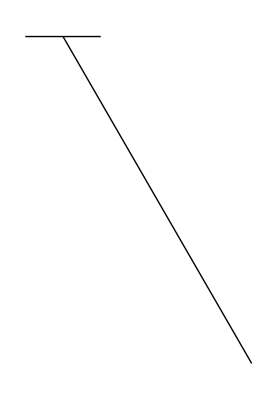

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}]
}, ImageSize->Tiny]
```

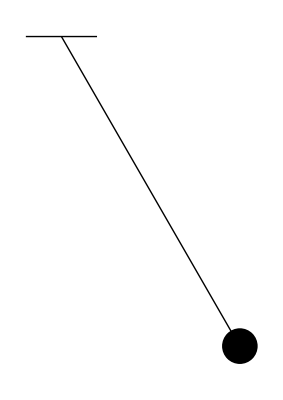

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05]
}, ImageSize->Tiny]
```

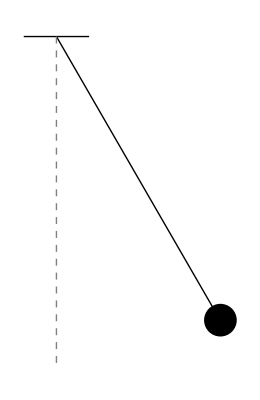

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05],
{Dashed, Gray, Line[{{0, 0}, {0, -1}}]}
}, ImageSize->Tiny]
```

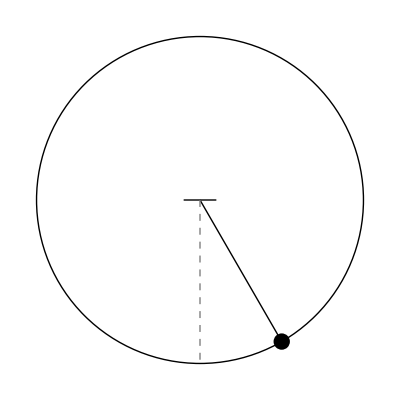

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05],
{Dashed, Gray, Line[{{0, 0}, {0, -1}}]},
Circle[{0, 0}, 1]
}, ImageSize->Tiny]
```

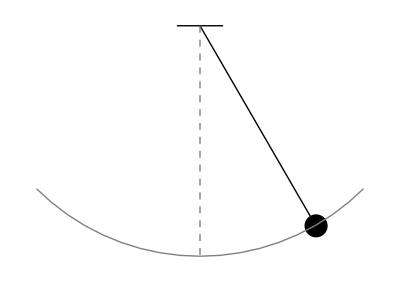

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05],
{Dashed, Gray, Line[{{0, 0}, {0, -1}}]},
{Gray, Circle[{0, 0}, 1, {-3 Pi/4, -Pi/4}]}
}, ImageSize->Tiny]
```

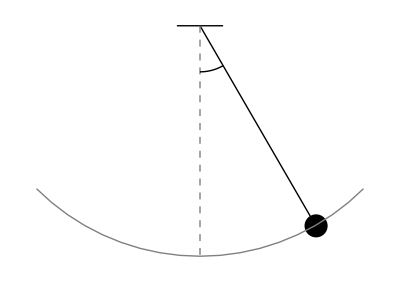

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05],
{Dashed, Gray, Line[{{0, 0}, {0, -1}}]},
{Gray, Circle[{0, 0}, 1, {-3 Pi/4, -Pi/4}]},
Circle[{0, 0}, .2, {-Pi/2, -Pi/3}]
}, ImageSize->Tiny]
```

```mathematica
?Text
```

Text[expr] displays with expr in plain text format. 
Text[expr,coords] is a graphics primitive that displays the textual form of expr centered at the point specified by coords.

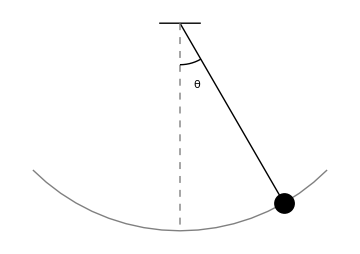

```mathematica
Graphics[{
Line[{{0, 0}, {Cos[Pi/3], -Sin[Pi/3]}}],
Line[{{-0.1, 0}, {0.1, 0}}],
{Dashed, Gray, Line[{{0, 0}, {0, -1}}]},
{Gray, Circle[{0, 0}, 1, {-3 Pi/4, -Pi/4}]},
Circle[{0, 0}, .2, {-Pi/2, -Pi/3}],
{FontSize->18, Text["θ", {0.08, -0.3}]},
Disk[{Cos[Pi / 3], -Sin[Pi / 3]}, 0.05]
}, ImageSize->Medium]
```

```mathematica
?Polygon
```

Polygon[{p_1,…,p_n}] represents a filled polygon with points p_i.
Polygon[{{p_11,…},{p_21,…},…}] represents a collection of polygons.

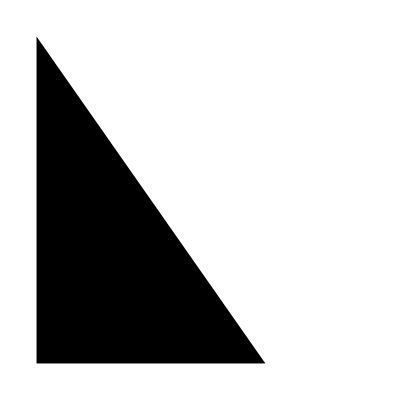

```mathematica
Graphics[Polygon[{{0, 0}, {1, 0}, {0.7, 0}, {0, 1}}], ImageSize->Tiny]
```

```mathematica
Triangle
```

Triangle

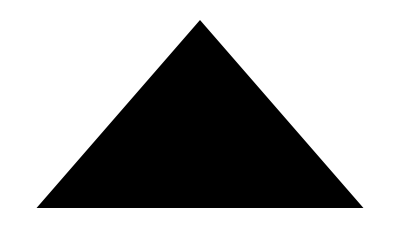

```mathematica
Graphics[Triangle[{{0, 0}, {1, 0}, {0.5, Sqrt[3]/3}}], ImageSize->Tiny]
```

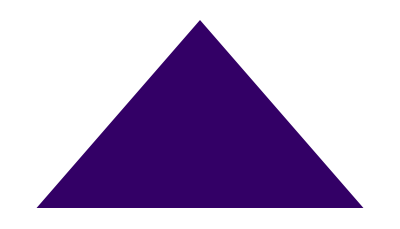

```mathematica
Graphics[{RGBColor[0.2, 0, 0.4], Triangle[{{0, 0}, {1, 0}, {0.5, Sqrt[3]/3}}]}, ImageSize->Tiny]
```

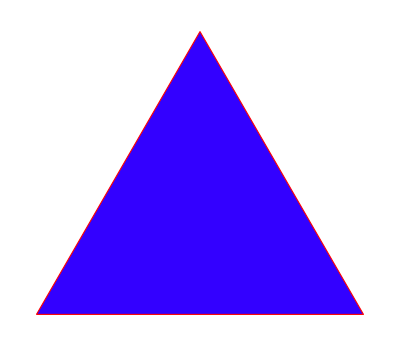

```mathematica
Graphics[{EdgeForm[{Red, Dashed, Thick}],RGBColor[0.2, 0, 4], Triangle[{{0, 0}, {1, 0}, {0.5, Sqrt[3]/2}}]}, ImageSize->Tiny]
```

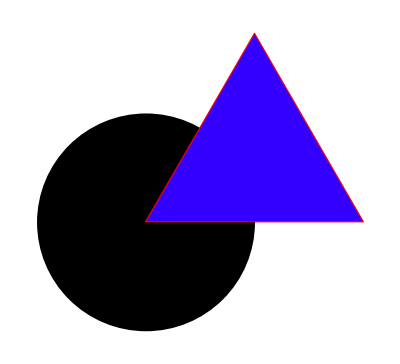

```mathematica
Graphics[{
Disk[{0, 0}, 0.5],
{EdgeForm[{Red, Dashed, Thick}],RGBColor[0.2, 0, 4], Triangle[{{0, 0}, {1, 0}, {0.5, Sqrt[3]/2}}]}
}, ImageSize->Tiny]
```

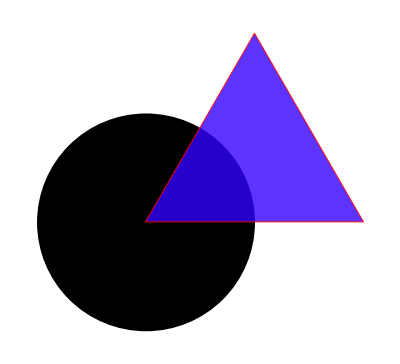

```mathematica
Graphics[{
Disk[{0, 0}, 0.5],
{EdgeForm[{Red, Dashed, Thick}],RGBColor[0.2, 0, 4],Opacity[0.8], Triangle[{{0, 0}, {1, 0}, {0.5, Sqrt[3]/2}}]}
}, ImageSize->Tiny]
```